```mathematica
Clear["`*"]
SetDirectory[NotebookDirectory[]]
```

## Loader/Writer

```mathematica
Clear[snapshotReader]
snapshotReader[wd_String?DirectoryQ,infix_String,types:{__String}]:=With[{path=FileNameJoin[{wd,"snapshot-"<>infix<>".snapshot"}]},
Module[{is,header,dE},
is=OpenRead[path,BinaryFormat->True];
header=BinaryRead[is,{"UnsignedInteger64","UnsignedInteger64"}];
dE=BinaryReadList[is,types];
Close[is];
{header,dE}
]
]
```

```mathematica
Clear[snapshotWriter]
snapshotWriter[wd_String?DirectoryQ,infix_String,header:{_Integer,_Integer},data:{__Real}]:=With[{path=FileNameJoin[{wd,"snapshot-"<>infix<>".snapshot"}]},
Module[{os},
os=OpenWrite[path,BinaryFormat->True];
BinaryWrite[os,header,{"UnsignedInteger64","UnsignedInteger64"}];
BinaryWrite[os,data,"Real64"];
Close[os]
]
]
```

## Parse Inputs.h

```mathematica
inputs=With[{src=FileNameJoin[{".","Inputs.h"}],filter={"c","Dx","Nx","dt"}},
Module[{data},
data=StringTrim/@ReadList[src,String];
data=DeleteCases[data,_String?(StringFreeQ["="~~__~~";"])];
data=Join@@Map[StringCases[#,$1__~~"="~~$2__~~";":>Rule[StringSplit[$1,Whitespace]//Last,StringTrim[$2]]]&,data];
Thread[Rule[filter,Map[ToExpression,filter/.data]]]//Association
(*(*initial phase ϕ0; the phase argument is ϕ(x)-ϕ0*)
data["Eϕ0"]=0;
(*phase correction in B due to B lagging E by half a grid size and by half a time step*)
data["Bϕ0"]=data["Eϕ0"]+data["Dx"]/2-data["dt"]/2;
data*)
]
]
```

## Prob 14.2

Consider a plane electromagnetic harmonic wave traveling towards the positive x direction in free space, having angular frequency ω=c (thus 𝕜=1 𝕩̂).
Consider the fluctuating electric field is given by
𝔼=𝕪̂ E_0 ⅇ^(ⅈ(k x-ω t)).
From Faraday's law, the fluctuating magnetic field is given by
𝔹=c/ω 𝕜×𝔼=(c k)/ω E_0 𝕫̂ ⅇ^(ⅈ(k x-ω t))=E_0 𝕫̂ ⅇ^(ⅈ(k x-ω t)).

```mathematica
{Ey0,Bz0}=With[{inputs=inputs,k=1,E0=1},
Module[{x,Ey,Bz,ϕ0,ω},
ω=k inputs["c"];
x=Range[inputs["Nx"]]inputs["Dx"];
Ey=E0 Exp[I(k x)]//Re;
(*phase difference; B is lagging E by half a grid size and half a time step*)
ϕ0=k inputs["Dx"]/2-ω inputs["dt"]/2;
Bz=E0 Exp[I(k x-ϕ0)]//Re;
Show[
ListPlot[
Take[{Ey,Bz},All,50],
Joined->True
]
]//Print;
{Ey,Bz}
]
];
```

```mathematica
With[{Ey=Ey0,Bz=Bz0,wd=FileNameJoin[{"./01_prob_14_2"}]},
Module[{header,𝔹,𝔼},
{header,𝔹}=snapshotReader[wd,"bfield",{"Real64","Real64","Real64"}];
{header,𝔼}=snapshotReader[wd,"efield",{"Real64","Real64","Real64"}];
𝔹[[All,3]]=Bz;
𝔼[[All,2]]=Ey;
{snapshotWriter[wd,"bfield",header,𝔹//Flatten],
snapshotWriter[wd,"efield",header,𝔼//Flatten]}
]
]
```

## Prob 14.4 & 14.6

The electric field vector of an elliptically polarized plane wave, propagating in free space, can be expressed as
𝔼=((𝕖̂)_1 E_1^0 ⅇ^(ⅈ α_1)+(𝕖̂)_2 E_2^0 ⅇ^(ⅈ α_2))ⅇ^(ⅈ(𝕜·𝕣-ω t)).
By Faraday's law, the magnetic field vector is
𝔹=((𝕖̂)_2 E_1^0 ⅇ^(ⅈ α_1)-(𝕖̂)_1 E_2^0 ⅇ^(ⅈ α_2))ⅇ^(ⅈ(𝕜·𝕣-ω t)).
For simplicity, let us assume E^0=E_1^0=E_2^0=1/√2 and α_2=α_1+π/2 (that is, righthand circular polarization).

```mathematica
{Ey0,Ez0,By0,Bz0}=With[{inputs=inputs,k=1,E0=1/√2,α1=0,α2=Pi/2},
Module[{x,Ey,Ez,By,Bz,ϕ0,ω},
ω=k inputs["c"];
x=Range[inputs["Nx"]]inputs["Dx"];
Ey=E0 Exp[I(k x+α1)]//Re;
Ez=E0 Exp[I(k x+α2)]//Re;
(*phase difference; B is lagging E by half a grid size and half a time step*)
ϕ0=k inputs["Dx"]/2-ω inputs["dt"]/2;
Bz=E0 Exp[I(k x+α1-ϕ0)]//Re;
By=-E0 Exp[I(k x+α2-ϕ0)]//Re;
Show[
ListPlot[
Take[{Ey,Ez,By,Bz},All,40],
Joined->True,
PlotLabels->{"Ey","Ez","By","Bz"}
]
]//Print;
{Ey,Ez,By,Bz}
]
];
```

```mathematica
With[{Ey=Ey0,Ez=Ez0,By=By0,Bz=Bz0,wd=FileNameJoin[{"./02_prob_14_4"}]},
Module[{header,𝔹,𝔼},
{header,𝔹}=snapshotReader[wd,"bfield",{"Real64","Real64","Real64"}];
{header,𝔼}=snapshotReader[wd,"efield",{"Real64","Real64","Real64"}];
𝔹[[All,3]]=Bz;
𝔹[[All,2]]=By;
𝔼[[All,2]]=Ey;
𝔼[[All,3]]=Ez;
{snapshotWriter[wd,"bfield",header,𝔹//Flatten],
snapshotWriter[wd,"efield",header,𝔼//Flatten]}
]
]
```

## Prob 14.12

Consider a one-dimensional wave packet at the instant t=0, whose amplitude function A(k) is given by the Gaussian function
A(k)=ⅇ^(-(a^2(k-k_0))^2),
where a and k_0 are constants.
The finite simulation size means that the system can only afford a certain number of harmonics dictated by the grid size, Δx, and the number of grid points, N_x.
k_i=i Δk, where 0≤i≤N_x/2 and Δk=(2π)/(Δx N_x).
Expressing A(k) in terms of i,
A(k)=ⅇ^(-a^2Δ(k^2(i-i_0))^2).

For a single harmonic, consider the electric field of prob. 14.2:
𝔼=𝕪̂ E_0 ⅇ^(ⅈ(k x-ω t)).
From Faraday's law, the magnetic field is given by
𝔹=𝕫̂ E_0 ⅇ^(ⅈ(k x-ω t)).
Assume E_0=1.

```mathematica
{2Pi/(inputs["Dx"]inputs["Nx"]),Pi/inputs["Dx"],inputs["Nx"]/2}
```

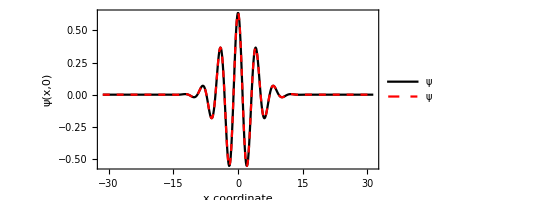

```mathematica
dynamic=With[{inputs=inputs,kfwhm=.6},
Module[{Δk,ilist,ks,i0,a,Ak,ωs,x,ψ1,ψ2},
Δk=2Pi/(inputs["Nx"]inputs["Dx"]);
ilist=Range[0,inputs["Nx"]/2];
i0=15;
a=1/Divide[kfwhm,2 √Log[2]];
Ak=Exp[-a^2Δk^2(ilist-i0)^2]//Chop;
ks=Δk*ilist;
ωs=ks*inputs["c"];
(*ListPlot[Thread[{ks,Ak}],Joined->True]*)
ψ1=Total[Ak Exp[I ks x]Δk];
x=Range[inputs["Nx"]]inputs["Dx"];
x-=Mean[x];
ψ1=ψ1//Chop//Re;
ψ2=Sqrt[Pi]/a Exp[I Δk i0 x]Exp[-x^2/(4a^2)]//Chop//Re;
Show[
ListPlot[
{Thread[{x,ψ1}],Thread[{x,ψ2}]},
Joined->True,
PlotRange->All,
PlotStyle->Thread[Directive[{Black,Red},{Dashing[{}],Dashed}]],
PlotLegends->Placed[{"\!\(ψ(x)=∫_(-∞)^∞ A(k)ⅇ^(ⅈ k x)ⅆ k\)","\!\(ψ(x)=(√π)/aⅇ^(ⅈ SubscriptBox[k, 0] x)exp(-x^2/(4 SuperscriptBox[a, 2]))\)"},Above]
],
BaseStyle->13,
AspectRatio->1/2,
FrameLabel->{"x coordinate","ψ(x,0)"},
Frame->True,
Axes->False
]
]
]
```

```mathematica
Export[FileNameJoin[{"./figures","initial_wave_packet.png"}],dynamic]
```

./figures/initial_wave_packet.png

```mathematica
{Ey0,Bz0}=With[{inputs=inputs,kfwhm=.6,E0=1},
Module[{Δk,ilist,ks,i0,a,Ak,ωs,x,ϕ0,Ey,Bz},
Δk=2Pi/(inputs["Nx"]inputs["Dx"]);
ilist=Range[0,inputs["Nx"]/2];
i0=15//Round;
a=1/Divide[kfwhm,2 √Log[2]];
Ak=Exp[-a^2Δk^2(ilist-i0)^2]//Chop;
ks=Δk*ilist;
ωs=ks*inputs["c"];
(*ListPlot[Thread[{ks,Ak}],Joined->True]*)
Ey=E0 Total[Ak Exp[I(ks x)]Δk];
ϕ0=ks inputs["Dx"]/2-ωs inputs["dt"]/2;
Bz=E0 Total[Ak Exp[I(ks x-ϕ0)]Δk];
x=Range[inputs["Nx"]]inputs["Dx"];
(*x-=Mean[x];*)
Ey=Ey//Chop//Re;
Bz=Bz//Chop//Re;
ListPlot[{Thread[{x,Ey}],Thread[{x,Bz}]},Joined->True,PlotRange->All]//Print;
{Ey,Bz}
]
];
```

```mathematica
With[{Ey=Ey0,Bz=Bz0,wd=FileNameJoin[{"./03_prob_14_12"}]},
Module[{header,𝔹,𝔼},
{header,𝔹}=snapshotReader[wd,"bfield",{"Real64","Real64","Real64"}];
{header,𝔼}=snapshotReader[wd,"efield",{"Real64","Real64","Real64"}];
𝔹[[All,3]]=Bz;
𝔼[[All,2]]=Ey;
{snapshotWriter[wd,"bfield",header,𝔹//Flatten],
snapshotWriter[wd,"efield",header,𝔼//Flatten]}
]
]
```